Define expected reward function R(t,s,cx_d) in terms of decision rule boundary t, shape parameter s, and impact of distractor cx_d.

```mathematica
x={6,12,18,24,32,38,44,50};

R[t_,s_,cxd_]:=Total[(1/(1+Exp[(-1/s) (t-#)])+1/(1+Exp[(-1/s) (t-#-cxd)]))&/@x[[1;;4]]]+Total[(1/(1+Exp[(1/s) (t-#)])+1/(1+Exp[(1/s) (t-#-cxd)]))&/@x[[5;;8]]];
```

Hypothesis:  t* = 28+0.5cxd maximizes R

```mathematica
tstar[cxd_]:=28+0.5 cxd;
```

Compute first and second partial derivatives of R

```mathematica
dRdt[t_,s_,cxd_]:=D[R[u,s,cxd],u]/.u->t;

d2Rdt2[t_,s_,cxd_]:=D[R[u,s,cxd],{u,2}]/.u->t;
```

Evaluate both at t=t*

```mathematica
dRdtAt[s_,cxd_]:=dRdt[tstar[cxd],s,cxd];

d2Rdt2At[s_,cxd_]:=d2Rdt2[tstar[cxd],s,cxd];
```

```mathematica
Assuming[s>0,FullSimplify[dRdtAt[s,cxd]]]
```

0

Confirmed: dR/dt = 0 at t =t*, regardless of values of s, cxd
Determine convexity:

```mathematica
signAt[s_?NumericQ,cxd_?NumericQ]:=Sign@N[d2Rdt2At[s,cxd]];
```

General::munfl: Exp[-8610.07] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4305.04] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

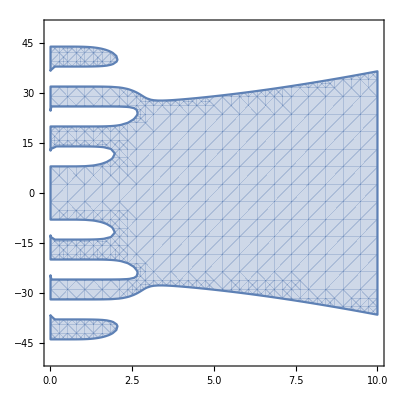

```mathematica
RegionPlot[s>0&&-44<cxd<44&&d2Rdt2At[s,cxd]<0,{s,0.01,10},{cxd,-50,50}]
```

In the shaded (s,cxd) region, R has a local max at t=t*

```mathematica
Plot3D[ R[t,s,cxd]/.t->tstar[cxd], {s,0.01,10},{cxd,-50,50}]
```

General::munfl: Exp[-4386.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3826.33] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-3266.33] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[ R[t,s,cxd]/.cxd->10, {t,20,50},{s,0.001,10}]
```

General::munfl: Exp[-8164.86] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4666.17] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1167.48] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics3D-

```mathematica
Plot3D[ R[t,s,cxd]/.s->1, {t,6,50},{cxd,-50,50}, MeshFunctions->{#3&}]
```

-Graphics3D-

```mathematica
dRdt[t,s,cxd]
```

-ⅇ^((-50+t)/s)/((1+ⅇ^((-50+t)/s))^2 s)-ⅇ^((-44+t)/s)/((1+ⅇ^((-44+t)/s))^2 s)-ⅇ^((-38+t)/s)/((1+ⅇ^((-38+t)/s))^2 s)-ⅇ^((-32+t)/s)/((1+ⅇ^((-32+t)/s))^2 s)+ⅇ^(-(-24+t)/s)/((1+ⅇ^(-(-24+t)/s))^2 s)+ⅇ^(-(-18+t)/s)/((1+ⅇ^(-(-18+t)/s))^2 s)+ⅇ^(-(-12+t)/s)/((1+ⅇ^(-(-12+t)/s))^2 s)+ⅇ^(-(-6+t)/s)/((1+ⅇ^(-(-6+t)/s))^2 s)-ⅇ^((-50-cxd+t)/s)/((1+ⅇ^((-50-cxd+t)/s))^2 s)-ⅇ^((-44-cxd+t)/s)/((1+ⅇ^((-44-cxd+t)/s))^2 s)-ⅇ^((-38-cxd+t)/s)/((1+ⅇ^((-38-cxd+t)/s))^2 s)-ⅇ^((-32-cxd+t)/s)/((1+ⅇ^((-32-cxd+t)/s))^2 s)+ⅇ^(-(-24-cxd+t)/s)/((1+ⅇ^(-(-24-cxd+t)/s))^2 s)+ⅇ^(-(-18-cxd+t)/s)/((1+ⅇ^(-(-18-cxd+t)/s))^2 s)+ⅇ^(-(-12-cxd+t)/s)/((1+ⅇ^(-(-12-cxd+t)/s))^2 s)+ⅇ^(-(-6-cxd+t)/s)/((1+ⅇ^(-(-6-cxd+t)/s))^2 s)

```mathematica
tempexpr = d2Rdt2At[s,cxd];
```

```mathematica
Cancel[tempexpr*s^2]
```

(2 ⅇ^(4/s-1/s) (2678+ⅇ^1+ⅇ^(6.513/s)+ⅇ^((7.5 cxd)/s)))/((1+ⅇ^(4/s+1))^3 (1+ⅇ^1)^3 (1+1)^3 1^3 1 (1)^3 (ⅇ^1+1)^3 (ⅇ^(22/s)+ⅇ^(1/s))^3)
 |  |  |  |

```mathematica
Factor[%32]
```

(2 ⅇ^(-44/s) (3632+ⅇ^1+ⅇ^(216./s+1)+ⅇ^(222./s+1/s)))/((1+ⅇ^(4./s+1))^3 (1+ⅇ^1)^3 (1+1)^3 3 1^3 (ⅇ^1+1)^2 (ⅇ^(22./s)+ⅇ^(1/s))^3)
 |  |  |  |

$Aborted

```mathematica
Ldd[z_]:=LogisticSigmoid[z](1-LogisticSigmoid[z])(1-2LogisticSigmoid[z]);
```

```mathematica
x={6,12,18,24,32,38,44,50}
```

```mathematica
StabConv[s_,cxd_]:= Total[ (Ldd[(28-0.5cxd-#)/s]+Ldd[(28+0.5cxd-#)/s])&/@x[[1;;4]]];
```

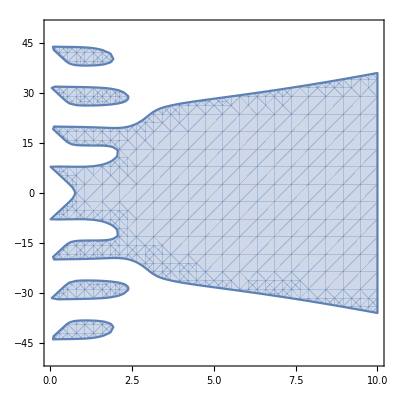

```mathematica
RegionPlot[s>0&&-44<cxd<44&&StabConv[s,cxd]<-0.01,{s,0.01,10},{cxd,-50,50}]
```